# single photon imaging

P. Huft

Calculations for the quantum optics lab I’m setting up for the HQAN TeachQuantum program.

Coherent laser light photon stats. Attenuate to approximately a single photon state. For a calculation of the state of the light after the double slit (or equivalently, a NPBS) for a coherent state truncated beyond |2>, see my turquoise Leuchtturm journal page 225.

time of flight (τ) to detector from the final attenuation stage

3.33333×10^-11

laser power with mean of n=0.05 photons/τ

3.94161×10^-10

Probability of 2 photons per τ

0.00118904

readout time t

0.5

Photons/readout

7.5×10^8

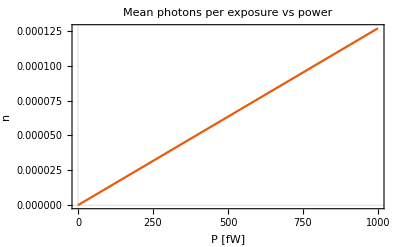

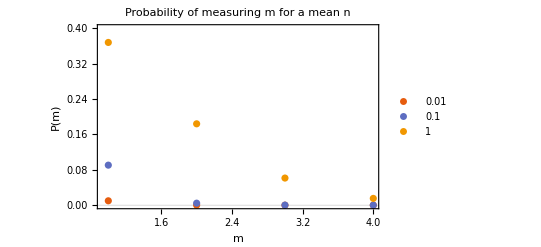

0.05

number state amplitudes, n=0.05

{{1,0.218086},{2,0.0344824},{3,0.00445166},{4,0.000497711}}

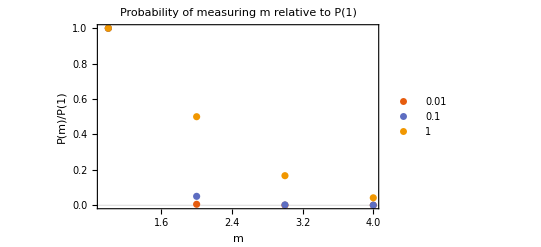

```mathematica
h=6*10^-34;
λ=6.85*10^-7;
c=3*10^8;
"time of flight (τ) to detector from the final attenuation stage"
τ=0.01/c
ν=c/λ;
n=.05;(*mean number of photons per exposure τ in our coherent state*)
α=√n;
Print["laser power with mean of n=",n," photons/τ"](*that is, there is at most one photon at a time in the region following the attenuation stages. not a strictly correct way of thinking abou this.*)
P=(n h ν)/τ
"Probability of 2 photons per τ"
m=2;
ⅇ^-n(n^m/(m!))//N 
"readout time t"
t=0.5
"Photons/readout"
P/(h ν) t
Clear[n,m]
nsteps={0.01,0.1,1};(*mean photons*)
Plot[P*10^-15/((h ν)/τ),{P,0.1,1000},PlotLabel->"Mean photons per exposure vs power" ,PlotTheme->"Scientific",FrameLabel->{"P [fW]","n"}]
ListPlot[Evaluate[Table[Table[{m,ⅇ^-n n^m/(m!)},{m,Range[4]}],{n,nsteps}]],PlotLegends->nsteps,PlotRange->{0,0.4},PlotLabel->"Probability of measuring m for a mean n" ,PlotTheme->"Scientific",FrameLabel->{"m","P(m)"}]
n=0.05
Print["number state amplitudes, n=",n]
Table[{m,ⅇ^(-n/2)n^(m/2)/(√(m!))},{m,Range[4]}]
Clear[n]

ListPlot[Evaluate[Table[Table[{m,n^(m-1)/(m!)},{m,Range[4]}],{n,nsteps}]],PlotLegends->nsteps,PlotRange->All,PlotLabel->"Probability of measuring m relative to P(1)" ,PlotTheme->"Scientific",FrameLabel->{"m","P(m)/P(1)"}]
```

Choose how much to attenuate the beam with the polarizers and fiber.

```mathematica
f=0.02;
A1=0.005;
A2=0.0005;
A3=0.0004;
Pin=2*^-4;
Pout=2.6*^-15;
A4 = Pout/(Pin A1 A2 A3 f)
```

0.65

SNR calculation. All values are per pixel, and noise values are taken from the manual, so they are probably optimistic for the used camera.

Formulas come from the Hamamatsu EM-CCD Technical Note. Example calculation of the noise vs input photon number showing that readout noise is the dominant noise source for fewer than 70 photons.

```mathematica
Clear[n,d,τ];
τ=.10;
QE=0.9;(*quantum efficiency @ 685nm*)
σr = 8;(*readout noise*)
d=0.01;(*dark electrons/s, air cooling to -65 C*)
σd = √(τ d);(*dark current noise*)
σs=√(QE n);(*photon shot noise*)
σcic =0.01;(*spurious noise from clock-induced charge*)
σ=√(σr^2+σd^2+σs^2+σcic^2);
"σd, σs, σcic RMS counts/s"
Print[σd," ",σs," " ,σcic]
"SNR"
(QE n)/σ
```

σd, σs, σcic RMS counts/s

0.0316228 0.948683 √n 0.01

SNR

(0.9 n)/(√(64.0011+0.9 n))

```mathematica
σr
```

0.8

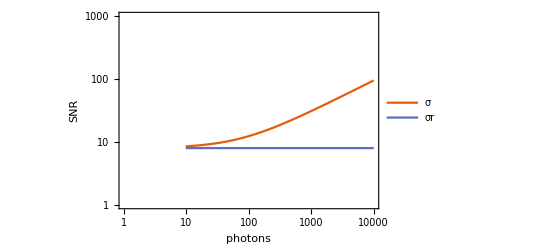

```mathematica
LogLogPlot[{√(σr^2+d τ+QE n+σcic^2),σr},{n,0,10000},PlotLegends->{"σ","σr"},PlotRange->{{1,10000},{1,1000}},PlotTheme->"Scientific",FrameLabel->{"photons","SNR"}]
```

How SNR depends on EM gain. This multiplies not only e^- from real detection events but from spurious/dark clicks too. The EM gain has excess noise proportional to the EM gain which amplifies the dark noise and c.i.c. as well. At large EM gain M, this factor is ultimately what limits the SNR.

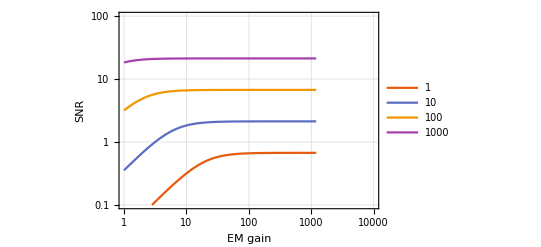

```mathematica
Clear[τ,σr,n,M];
τ=.033;
σr =25;(*number of e^-. readout noise. this technically depends on EM gain. at 1200 should have σr=1.*)
F=1.41;(*excess noise; Hamamatsu's unqualified estimate*)
σ = √(σr^2+F^2 M^2(d τ+QE n+σcic^2));
nsteps = {1,10,100,1000};(*mean photons per pixel*)
LogLogPlot[Evaluate[Table[(QE n M)/σ,{n,nsteps}]],{M,1,1200},PlotRange->{{1,10^4},{0.1,100}},PlotLegends->nsteps,GridLines->Automatic,PlotTheme->"Scientific",FrameLabel->{"EM gain","SNR"}]
```

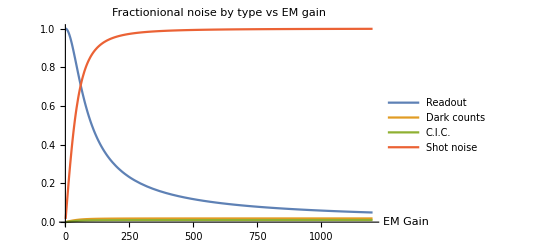

```mathematica
Plot[Evaluate[{σr/(√(σr^2+F^2 M^2(d τ+QE n+σcic^2))),(F M √(d τ))/(√(σr^2+F^2 M^2(d τ+QE n+σcic^2))),(F M σcic)/(√(σr^2+F^2 M^2(d τ+QE n+σcic^2))),(F M √(QE n))/(√(σr^2+F^2 M^2(d τ+QE n+σcic^2)))}/.n->1],{M,1,1200},PlotLegends->{"Readout","Dark counts","C.I.C.","Shot noise"},PlotLabel->"Fractionional noise by type vs EM gain",AxesLabel->{"EM Gain",""}]
```

In all of the above examples, we have a much larger number of photons incident per pixel per frame than for a single photon imaging experiment. Below I try to make realistic estimates for one photon per frame (!= 1 per pixel per frame).

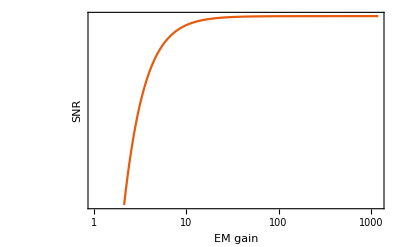

```mathematica
Clear[τ,σr,n]
τ=10^-5;
F=1.41;(*excess noise; Hamamatsu's unqualified estimate*)
σr=1;(*readout noise in EMCCD mode*)
n=1; (*is n=1 one photon per frame or per pixel per frame?*)
σ = √(σr^2+F^2 M^2(d τ+QE n+σcic^2));
LogLogPlot[(QE n M)/σ,{M,1,1200},PlotRange->Automatic,GridLines->Automatic,PlotTheme->"Scientific",FrameLabel->{"EM gain","SNR"}]
```

```mathematica
Clear[n]
Plot[(QE n)/□]
```

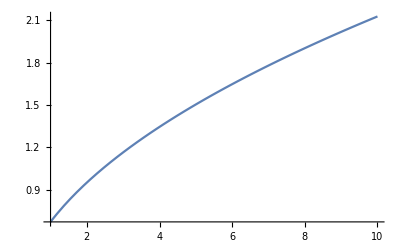

```mathematica
Plot[(QE n)/(√(F^2(QE n))),{n,1,10}]
```

How does the noise vary with EM gain and exposure time?

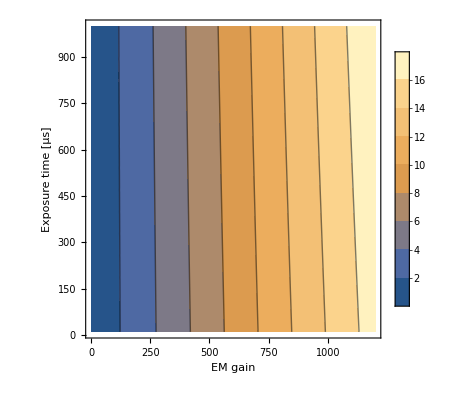

```mathematica
Clear[τ];
F=1.41;(*excess noise; Hamamatsu's unqualified estimate*)
σr=1;(*readout noise in EMCCD mode? this is really a function of EM gain and the most optimistic case*)
n=0; (*no incident light, e.g. if the camera is capped.*)
σ = √(σr^2+F^2 M^2(d 10^-6 τ+QE n+σcic^2));
ContourPlot[σ,{M,1,1200},{τ,10,1000},FrameLabel->{"EM gain","Exposure time [μs]"},PlotLegends->Automatic]
```

## misc

```mathematica
Δν=10^5;
lcoh = 1/2 c/Δν
```

1499.35

```mathematica
λ=8.05*^-7;
Δλ=2*^-9;
"coherence length"
lcoh = (1/2)(λ^2/Δλ)
(*lcoh=(1/2)(c/Δν)*)
"temporal coherence"
tcoh = lcoh/c
```

```mathematica
0.1/c
```

3.33478×10^-10

```mathematica
λ=6.85*10^-7;
λ^2/c 10^5
```

1.56476×10^-16

```mathematica
((6.85*^-7)^2)/c*10^5
```

```mathematica
c/((8.05*^-7)^2)2*10^-9
```

9.25489×10^11

```mathematica
n=1; (*mean number of photons detected in time τ*)
l = 0.01;  (*some free path in the apparatus. just helps to conceptualize*)
"detection time"
τ =10^-5//N
"photon travel length in this time (we want only one photon per this path length during τ)"
c τ
Print["power for n= ",n," photons per detection time"]
(n(h c)/λ)/τ
```

```mathematica
"detection time"
```

0.00001

photon travel length in this time (we want only one photon per this path length during τ)

3000.

power for n= 1 photons per detection time

2.23602×10^-14

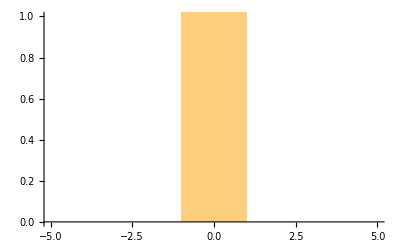

```mathematica
data=RandomVariate[ProbabilityDistribution[(Sinc[(2π)/512 x/0.5]Cos[(2π)/512 x/0.05])^2,{x,-256,256}],100000];
Histogram[data,512,PlotRange->]
```

```mathematica
click[x_]:=Module[{f,y},
y=RandomReal[];
f=(Sinc[(2π)/512 x/0.5]Cos[(2π)/512 x/0.05])^2;
If[y<f,1,0]
]
```

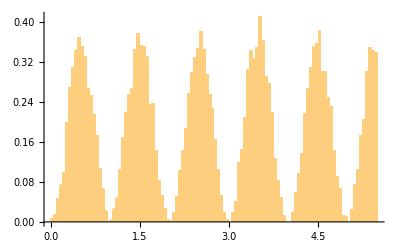

```mathematica
Histogram[RandomVariate[ProbabilityDistribution[(Sin[π x])^2,{x,0,15}],10000],100,"PDF"]
```

```mathematica
0.005*0.0004*0.0005*0.0015
```

1.5×10^-12